Remove::rmnsm: There are no symbols matching "Global`*".

File:3

Max Y=0.0000418029; Min Y=-0.0000441184; Isw(uA)=1000000 Isw

Max X=0.0000592009; Min X=0.0000392175

File:121

Max Y=0.000040419; Min Y=-0.0000437038; Isw(uA)=1000000 Isw

Max X=0.0000619487; Min X=0.0000442134

File:143

Max Y=0.0000395397; Min Y=-0.0000429194; Isw(uA)=1000000 Isw

Max X=0.0000377188; Min X=0.0000333474

File:145

Max Y=0.0000386904; Min Y=-0.0000418578; Isw(uA)=1000000 Isw

Max X=0.0000403416; Min X=0.0000342217

File:147

Max Y=0.0000368406; Min Y=-0.0000402527; Isw(uA)=1000000 Isw

Max X=0.0000389677; Min X=0.0000350959

File:199

Max Y=0.0000347186; Min Y=-0.0000379222; Isw(uA)=1000000 Isw

Max X=0.0000379685; Min X=0.0000337221

File:201

Max Y=0.0000313064; Min Y=-0.0000346412; Isw(uA)=1000000 Isw

Max X=0.0000360951; Min X=0.0000323482

File:203

Max Y=0.0000214471; Min Y=-0.0000248556; Isw(uA)=1000000 Isw

Max X=0.0000375939; Min X=0.0000323482

File:205

Max Y=7.51102×10^-6; Min Y=-0.0000109409; Isw(uA)=1000000 Isw

Max X=0.0000361576; Min X=0.000032598

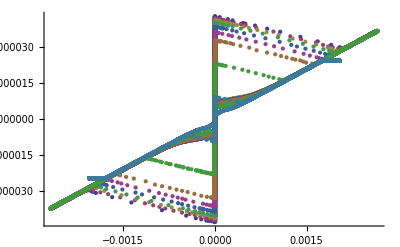

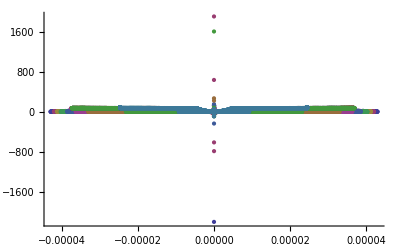

```mathematica
Remove["Global`*"]

(*Inputs*)
filelist={3,121,143,145,147,199,201,203,205};
inputpath="d:\\test\\";
rescaleV=100;
rescaleI=10000;
zeroposition=0;

outputpath=inputpath<>"Edited\\";
CreateDirectory[outputpath];
Is={};

(*Main cycle going through filelist*)
Do[
Print["\nFile:",k];

(*Load file with IV (current-voltage characteristics). Format - 4 columns. Column N2 - voltage, column N4 - current. N1,N3 - time. *)
file="iv"<>ToString[k];
rawdata=Map[{N[#[[2]]/rescaleV], N[#[[4]]/rescaleI]}&,Import[inputpath<>ToString[file]<>".txt","Table"]];

(*----SHIFT VERTICAL----*)
(*Select the central part of IV to find max/min Y values (current) for centering. We need selecting of middle - to exclude end parts of IV, that could be higher than central part *)
selectData = {};
leftX=-1*10^-4; rightX=1*10^-4;
For [ i = 1, i≤Length[rawdata], i++, If[rawdata[[i,1]] ≥leftX &&rawdata[[i,1]]≤ rightX,AppendTo[selectData, rawdata[[i]]] ]];

(*Find min/max Y*)
minY=Min[selectData[[All,2]]];
maxY=Max[selectData[[All,2]]];
Print["Max Y=",maxY,"; Min Y=", minY, "; Isw(uA)=",Isw*10^6];

(*Save switching current in list*)
Isw[k]=(Abs[maxY]+Abs[minY])/2;
AppendTo[Is,{Isw[k],k}];

(*Shift along Y axis to symmetrical position*)
yshiftData = {};
shiftY=zeroposition-(maxY+minY)/2;
For [ i = 1, i≤Length[rawdata], i++, AppendTo[yshiftData, rawdata[[i]]+{0,shiftY}]];

(*----SHIFT HORISONTAL----*)
(*Select part of Y-shifted data, that has near zero Y values. We need this to find min/max X values (voltage) exactly in the central part of IV, for centering by X*)
selectData = {};
minY2=-0.5*10^-6; maxY2=0.5*10^-6;
For [ i = 1, i≤Length[yshiftData], i++, If[yshiftData[[i,2]] ≥minY2 &&yshiftData[[i,2]]≤ maxY2,AppendTo[selectData, yshiftData[[i]]] ]];

(*Find min/max X*)
minX=Min[selectData[[All,1]]];
maxX=Max[selectData[[All,1]]];
Print["Max X=",maxX,"; Min X=", minX];

(*Shift along X to symmetrical position*)
xyshiftData = {};
shiftX=zeroposition-(maxX+minX)/2;
For [ i = 1, i≤Length[yshiftData], i++, AppendTo[xyshiftData, yshiftData[[i]]+{shiftX,0}]];

(*Convert IV to RI (resistance-current) presentation*)
riData=Map[{N[#[[2]]], N[#[[1]]/#[[2]]]}&,xyshiftData];

(*Export*)
Export[outputpath<>ToString[file]<>"_rescaled.dat",Map[{N[#[[1]]], N[#[[2]]]}&,rawdata]];
Export[outputpath<>ToString[file]<>"_shifted.dat",Map[{N[#[[1]]], N[#[[2]]]}&,xyshiftData]];
Export[outputpath<>ToString[file]<>"_RI.dat",Map[{N[#[[1]]], N[#[[2]]]}&,riData]],

{k,filelist}
];

(*Export list of switching currents*)
Export[outputpath<>"Isw"<>ToString[First[filelist]]<>"-"<>ToString[Last[filelist]]<>".dat",Is];

(*Overall list that will include all IV and RI data sets*)
ivAll={};
riAll={};
(*Import of shifted IVs *)
For[i=1, i<=Length[filelist], i++,
iv[i]=Map[{#[[1]], #[[2]]}&,Import[outputpath<>"iv"<>ToString[filelist[[i]]]<>"_shifted.dat", "Table"]];
ri[i]=Map[{#[[1]], #[[2]]}&,Import[outputpath<>"iv"<>ToString[filelist[[i]]]<>"_RI.dat", "Table"]];
AppendTo[ivAll,iv[i]];
AppendTo[riAll,ri[i]];
]

ListPlot[ivAll]
ListPlot[riAll]
```